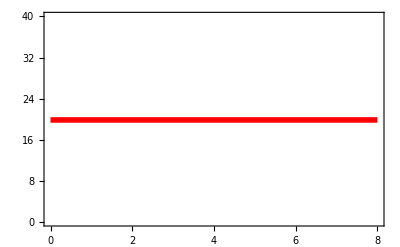
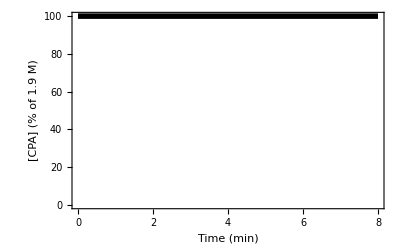
-Graphics--Graphics-CPA Exposure Profile 1

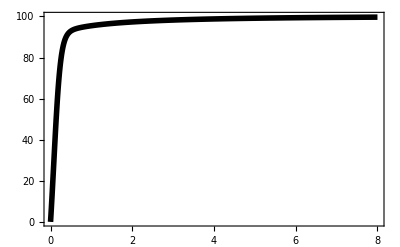
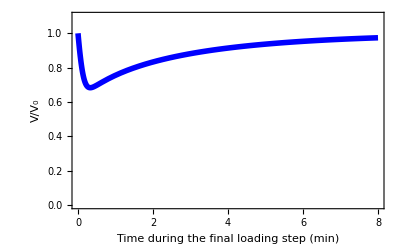
-Graphics--Graphics-Profile 1

-Graphics-

-Graphics-

```mathematica
(*Goals:
1. Plot Subscript[V, r](t)
2. Plot Subscript[C, i] (t)
3. Calculate min and max Vr
4. Calculate max Subscript[C, i]
5. Compare to Program 3 (min V/V0 = 0.68, max V/V0 = 1.0)
*)
(*Improvements from Program 3: 
1. Subscript[C, i] plot
2. Max Subscript[C, i] calculation
3. Fixed an error that can arise when plotting multiple profiles
4. Fixed an error for tabulated Subscript[C, e,Subscript[L, f]] value that arises for inputted profiles with at < 100% for the final loading step
*)
(*Conclusions: 
1. The program gives the same result as Program 3 (min V/V0 = 0.68, max V/V0 = 1.0) in addition to Subscript[C, i] info
*)

Clear["Global`*"]

(*inputs*)
profiles={
{{{100,t<8*60}},293,1}
}; (*enter in the format: {surroudning CPA concentration as a function of time (c=f(t)), temperature (T), step number of the final loading step (locLf)}*)
MVCPA=.071/1000; (*m^3/mol, molar volume of CPA, compare to 7.1E-5 m^3/mol for glycerol, compare to 7.1E-5 m^3/mol for DMSO*)
Vb=.25*V0; (*osmotically inactive cell volume, compare to .2V0 for oocytes (Newton 1999)*)
adhered=0; (*enter 1 if cell is adherent (2D), enter ≠ 1 if cell is nonadherent (3D)*)

(*concentration inputs (comment out the input type (either osmolarity or osmolality) you do not want)*)
(*osmolarity inputs*)
inputsOsmolal=0; (*recommended to set at 0; if set at 1, the program will attempt to convert osmolality inputs*)
Cmax=1.91*1000; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample*)
C0=0*1000;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Cn0=.297*1000;(*osmol/m^3, initial intracellular nonpenetrating osmolarity*)
Cne=.297*1000;(*osmol/m^3, extracellular nonpenetrating osmolarity, compare to .332 for Celsior*)
(*(*osmolality inputs*)
inputsOsmolal=1; (*recommended to set at 1; any value other than 1: the program will not convert osmolality inputs to osmolarity*)
Mmax=2; (*osmol/kg, max osmolality of CPA surrounding the sample*)
M0=0; (*osmol/kg, initial intracellular CPA osmolality*)
Mn0=.3; (*osmol/kg, initial intracellular nonpenetrating osmolality, compare to .326 for porcine myocardium (Tranum-Jensen 1981)*)
Mne=.3; (*osmol/kg, extracellular nonpenetrating osmolality, compare to .335 for Celsior (Ostrozka-Cieslik 2009)*)*)

(*geometry inputs and calculations (comment out the geometry that you do not want)*)
(*(*inputs for an elliptical geometry*)
Lcell=110/1000/1000; (*m, length of cell, compare to 110 um for rat ventricular myocytes (Boyett 1991)*)
R1cell = 25/1000/1000; (*m, major radius of cell, compare to 25 um for rat ventricular myocytes (Boyett 1991)*)
RRatio=1/3; (*ratio of minor radius to major radius, compare to 1/3 for rat ventricular myocytes (Boyett 1991)*)
(*equations for an elliptical geomtery*)
R2cell=R1cell*RRatio; (*m, minor radius of cell*)
A0=π*Lcell*(R1cell+R2cell)+2*π*R1cell*R2cell; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Lcell*R1cell*R2cell/4; (*m^3, initial cell volume*)*)
(*inputs for a spherical geometry*)
Dcell=100/1000/1000; (*m, cell diameter, compare to 20 um for mostly-detached D13 hiPSC-CM (my measurement)*)
(*equations for a spherical geometry*)
A0=π*Dcell^2; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Dcell^3/6; (*m^3, initial cell volume*)

(*key parameters*)
Lp=1.7*10^-13; (*m^2*s/kg*)
Ps=6.8*10^-7; (*m/s*)

(*constants*)
Rgas=8.3145; (*J/mol/K = N*m/mol/K = kg*m^2/mol/K/s^2, gas constant*)

(*convert to osmolarity if necessary*)
If[inputsOsmolal==1,
Mw=55.55; (*mol water/kg water*)
Cw=55.346; (*mol water/L water*)
Cmax=1000*Mmax*(Cw-Mne-Mmax)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample*)
Print["Max concentration of CPA surrounding the sample: "<>ToString[Mmax]<>" osmolal = "<>ToString[Cmax]<>" mM"];
C0=1000*M0*(Cw-Mn0-M0)/Mw;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Print["Initial intracellular CPA concentration: "<>ToString[M0]<>" osmolal = "<>ToString[C0]<>" mM"];
Cn0=1000*Mn0*(Cw-Mn0-M0)/Mw; (*osmol/m^3, initial intracellular nonpenetrating osmolarity*)
Print["Initial intracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
Cne=1000*Mne*(Cw-Mne)/Mw; (*osmol/m^3, extracellular nonpenetrating osmolarity*)
Print["Extracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
];

(*equations*)
If[adhered==1, (*if cell is adhered*)
A0=A0/2; (*assume half the cell membrane is exposed*)
]

(*initialization*)
VPlots={};
CPlots={};
colors={Blue,Green,Black, Red,Purple,Orange,Brown,Yellow};
table={{"Profile","C_(e, SubscriptBox[L, f]) (M)","T (°C)","t_tot (min)","Min V/V_0","Max V/V_0","Max C_i (M)"}};

(*execution*)
nProfiles=Length[profiles];
ttotmax=Max[profiles[[All,1]][[All,-1]][[All,2,2]]];
For[i=1,i<nProfiles+1,i++,
If[inputsOsmolal==1,(*if concentration unit is osmolality*)
Me=Piecewise[profiles[[i]][[1]]]*Mmax/100; (*mol/m^3 = mM, c=f(t)*)
Ce=1000*Me*(Cw-Mne-Me)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), extracellular CPA molarity*)
,(*if concentration unit is osmolarity*)
Ce=Piecewise[profiles[[i]][[1]]]*Cmax/100; (*mol/m^3 = mM, c=f(t)*)
];
T=profiles[[i]][[2]]; (*K, T=f(t)*)
locLf=profiles[[i]][[3]]; (*location of the final loading step*)
nSteps=Length[profiles[[i]][[1]]];(*number of c steps*)
ttot=Last[profiles[[i]][[1]]][[2,2]]; (*s, total simulation time*)
vnSol=NDSolve[{v'[t]==-Lp*A0*Rgas*T*(Cne+Ce-(Cn0*(V0-Vb))/(v[t]+n[t]*MVCPA)-n[t]/(v[t]+n[t]*MVCPA)),n'[t]==Ps*A0*(Ce-n[t]/(v[t]+n[t]*MVCPA)),v[0]==V0-Vb,n[0]==C0*(V0-Vb)},{v,n},{t,0,ttot},MaxStepSize->.1][[1]];
v[t_]:=Evaluate[v[t]/.vnSol[[1]]]; (*m^3, volume of intracellular water*)
n[t_]:=Evaluate[n[t]/.vnSol[[2]]];(*osmol = mol (true for CPA), amount of intracellular CPA*)
Vr[n_,v_]:=(v+MVCPA*n+Vb)/V0;(*ratio of cell volume to initial cell volume*)
Ci[n_,v_]:=n/(v+MVCPA*n);(*mol/m^3, intracellular [CPA]*)
(*initialization*)
Vmins={}; (*list of Vmin for each step*)
Vmaxs={}; (*list of Vmax for each step*)
tPriorSteps=0; (*s, time of all prior steps*)
For[j=1,j<nSteps+1,j++,
tCurrentStep=profiles[[i]][[1]][[j]][[2,2]]; (*s, time until the end of the current step*)
If[j≤locLf,(*if this is a loading step*)
AppendTo[Vmins,FindMinimum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
If[j==locLf, (*if this is the final loading step*)
t=tCurrentStep-1;
Cemax=Ce;
Cimax=Ci[n[t],v[t]];
Clear[t];
];
,(*if this is an unloading step*)
AppendTo[Vmaxs,FindMaximum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
];
tPriorSteps=tCurrentStep;
];
Vmin=If[Length[Vmins]>0,Min[Vmins],Min[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Vmax=If[Length[Vmaxs]>0,Max[Vmaxs],Max[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Ce=Ce/.t->t*60; (*for plotting in min*)
Print[Labeled[Overlay[{Plot[T-273.15,{t,0,ttot/60},PlotStyle->{Red,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,40},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},FrameLabel->{{None,"T (°C)"},{None,None}}],Plot[Floor[Ce*100/Cmax,.1],{t,0,ttot/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{True,True,False,False},FrameStyle->{Automatic,Black,Automatic,Automatic},FrameLabel->{{If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"],None},{"Time (min)",None}}]}],"CPA Exposure Profile "<>ToString[i],Top]];
If[i<nProfiles,(*if this is not the last profile*)
AppendTo[VPlots,Plot[If[t<ttot/60,Vr[n[t*60],v[t*60]]],{t,0,ttotmax/60},PlotRange->{{0,ttotmax/60},{0,Ceiling[1.1*Vmax,.1]}},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]]]];
AppendTo[CPlots,Plot[If[t<ttot/60,Ci[n[t*60],v[t*60]]/1000],{t,0,ttotmax/60},PlotRange->{{0,ttotmax/60},{0,Ceiling[Cmax/1000,.1]}},AxesLabel->{"t (min)","Intracellular [CPA] (M)"},PlotStyle->colors[[i]]]];
,(*if this is the last profile*)
AppendTo[VPlots,Plot[If[t<ttot/60,Vr[n[t*60],v[t*60]]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
AppendTo[CPlots,Plot[If[t<ttot/60,Ci[n[t*60],v[t*60]]/1000],{t,0,ttotmax/60},PlotRange->{0,Ceiling[Cmax/1000,.1]},AxesLabel->{"t (min)",If[inputsOsmolal==1,"[CPA] (molal)","[CPA] (M)"]},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
];
tL=If[locLf==1,0,profiles[[i]][[1]][[locLf-1]][[2,2]]]; (*s, time at beginning of final loading step*)
Print[Labeled[Overlay[{Plot[100*Ci[n[t*60],v[t*60]]/Cmax,{t,tL/60,tCurrentStep/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Black},FrameLabel->{{None,If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"]},{None,None}}],Plot[Vr[n[t*60],v[t*60]],{t,tL/60,tCurrentStep/60},PlotStyle->{Blue,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,Ceiling[1.1*Vmax,.1]},Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},FrameLabel->{{"V/V_0",None},{"Time during the final loading step (min)",None}}]}],"Profile "<>ToString[i],Top]];
AppendTo[table,{i,Round[Cemax/1000,.1],Round[T-273.15,.1],ttot/60,Round[Vmin,.01],Round[Vmax,.01],Round[Cimax/1000,.01]}];
Clear[v,n];
]; (*end of i loop*)
Show[VPlots]
Show[CPlots]
Dataset[AssociationThread[First@table->#]&/@Rest@table]
```